## Zadanie 1

#### Podpunkt a.

```mathematica
Limit[x^2-x,x->1]
```

0

#### Podpunkt b.

```mathematica
Limit[Sin[x]/x,x->0]
```

1

#### Podpunkt c.

```mathematica
Limit[(1+x/n)^n,n->∞]
```

ⅇ^x

#### Podpunkt d.

```mathematica
Limit[x/(x-1),x->1,Direction->"FromAbove"]
Limit[x/(x-1),x->1,Direction->"FromBelow"]
```

∞

-∞

#### Podpunkt e.

```mathematica
Limit[ArcTan[x],x->∞]
```

π/2

#### Podpunkt f.

```mathematica
Limit[Sin[x],x->∞]
```

Indeterminate

## Zadanie 2

#### Podpunkt a.

```mathematica
f[x_]:=x Sin[x]+Cos[x];

f'[x]
f''[x]
f'''[x]
```

x Cos[x]

Cos[x]-x Sin[x]

-x Cos[x]-2 Sin[x]

#### Podpunkt b.

```mathematica
f[x_]:=x/(x+2);

f'[x] // Simplify
f''[x] // Simplify
f'''[x] // Simplify
```

2/(2+x)^2

-4/(2+x)^3

12/(2+x)^4

#### Podpunkt c.

```mathematica
f[x_]:=(x^2-x)/(x+2);

f'[x] // Simplify
f''[x] // Simplify
f'''[x] // Simplify
```

(-2+4 x+x^2)/(2+x)^2

12/(2+x)^3

-36/(2+x)^4

## Zadanie 3

#### Podpunkt a.

```mathematica
f[x_,y_]:=(x^2-y-x)/(x^2+y^2);

Print["Pochodne cząstkowe 1. rzędu:"]
Print["f_x = ",Simplify[D[f[x,y], x]]]
Print["f_y = ",Simplify[D[f[x,y], y]]]

Print["\nPochodne cząstkowe 2. rzędu:"]
Print["f_xx = ",Simplify[D[f[x,y], x,x]]]
Print["f_xy = f_yx = ",Simplify[D[f[x,y], x,y]]]
Print["f_y = ",Simplify[D[f[x,y], y,y]]]

Print["\nPochodne cząstkowe 3. rzędu:"]
Print["f_xxx = ",Simplify[D[f[x,y], x,x,x]]]
Print["f_xxy = f_xyx = f_yxx = ",Simplify[D[f[x,y], x,x,y]]]
Print["f_yyx = f_yxy = f_xyy = ",Simplify[D[f[x,y], y,y,x]]]
Print["f_yyy = ",Simplify[D[f[x,y], y,y,y]]]

Print["\nGradient:"]
Print["∇f = ",MatrixForm[Simplify[∇_{x,y} f[x,y]]]]

Print["\nHesjan:"]
Print["H = ",
MatrixForm[
{{Simplify[D[f[x,y], x,x]],Simplify[D[f[x,y], x,y]]},
{Simplify[D[f[x,y], y,x]],Simplify[D[f[x,y], y,y]]}}
]
]
```

Pochodne cząstkowe 1. rzędu:

f_x = (x^2-y^2+2 x y (1+y))/((x^2+y^2)^2)

f_y = (2 x y+y^2-x^2 (1+2 y))/((x^2+y^2)^2)

Pochodne cząstkowe 2. rzędu:

f_xx = (-2 x^3+6 x y^2-6 x^2 y (1+y)+2 y^3 (1+y))/((x^2+y^2)^3)

f_xy = f_yx = (2 (-3 x^2 y+y^3+x^3 (1+2 y)-x y^2 (3+2 y)))/((x^2+y^2)^3)

f_y = -(2 (-x^3+x^4+3 x y^2+y^3-3 x^2 y (1+y)))/((x^2+y^2)^3)

Pochodne cząstkowe 3. rzędu:

f_xxx = (6 (x^4-6 x^2 y^2+y^4+4 x^3 y (1+y)-4 x y^3 (1+y)))/((x^2+y^2)^4)

f_xxy = f_xyx = f_yxx = -(2 (-12 x^3 y+12 x y^3+y^4 (3+2 y)+x^4 (3+6 y)-2 x^2 y^2 (9+8 y)))/((x^2+y^2)^4)

f_yyx = f_yxy = f_xyy = (-6 x^4+4 x^5+36 x^2 y^2-6 y^4+12 x y^3 (2+y)-8 x^3 y (3+4 y))/((x^2+y^2)^4)

f_yyy = (6 (-4 x^3 y+4 x y^3+y^4-2 x^2 y^2 (3+2 y)+x^4 (1+4 y)))/((x^2+y^2)^4)

Gradient:

∇f = ((x^2-y^2+2 x y (1+y))/((x^2+y^2)^2)
(2 x y+y^2-x^2 (1+2 y))/((x^2+y^2)^2))

Hesjan:

H = ((-2 x^3+6 x y^2-6 x^2 y (1+y)+2 y^3 (1+y))/((x^2+y^2)^3) | (2 (-3 x^2 y+y^3+x^3 (1+2 y)-x y^2 (3+2 y)))/((x^2+y^2)^3)
(2 (-3 x^2 y+y^3+x^3 (1+2 y)-x y^2 (3+2 y)))/((x^2+y^2)^3) | -(2 (-x^3+x^4+3 x y^2+y^3-3 x^2 y (1+y)))/((x^2+y^2)^3))

#### Podpunkt b.

```mathematica
f[x_,y_]:=Sin[x+y];

Print["Pochodne cząstkowe 1. rzędu:"]
Print["f_x = f_y = ",Simplify[D[f[x,y], x]]]

Print["\nPochodne cząstkowe 2. rzędu:"]
Print["f_xx = f_xy = f_yx = f_y = ",Simplify[D[f[x,y], x,x]]]

Print["\nPochodne cząstkowe 3. rzędu:"]
Print["f_xxx = f_xxy = f_xyx = f_yxx = f_yyx = f_yxy = f_xyy = f_yyy = ",Simplify[D[f[x,y], x,x,x]]]

Print["\nGradient:"]
Print["∇f = ",MatrixForm[Simplify[∇_{x,y} f[x,y]]]]

Print["\nHesjan:"]
Print["H = ",
MatrixForm[
{{Simplify[D[f[x,y], x,x]],Simplify[D[f[x,y], x,y]]},
{Simplify[D[f[x,y], y,x]],Simplify[D[f[x,y], y,y]]}}
]
]
```

Pochodne cząstkowe 1. rzędu:

f_x = f_y = Cos[x+y]

Pochodne cząstkowe 2. rzędu:

f_xx = f_xy = f_yx = f_y = -Sin[x+y]

Pochodne cząstkowe 3. rzędu:

f_xxx = f_xxy = f_xyx = f_yxx = f_yyx = f_yxy = f_xyy = f_yyy = -Cos[x+y]

Gradient:

∇f = (Cos[x+y]
Cos[x+y])

Hesjan:

H = (-Sin[x+y] | -Sin[x+y]
-Sin[x+y] | -Sin[x+y])

## Zadanie 4

#### Podpunkt a.

```mathematica
f[x_]:=(x^2+3)/(2x+1);

Subscript[x, 0]=0;

y=f'[Subscript[x, 0]](x-Subscript[x, 0])+f[Subscript[x, 0]];

Print["Styczna do wykresu funkcji f(x) w punkcie (0,3):"]
Print["y = ",y]

Plot[
{Callout[f[x],"f(x)",Left],
Callout[y,"-6x+3",Below]},
{x,-10,10},
PlotRange->{-10,10},
AspectRatio->1
]
```

Styczna do wykresu funkcji f(x) w punkcie (0,3):

y = 3-6 x

-Graphics-

#### Podpunkt b.

```mathematica
Print[
"Mianownik zeruje się w punkcie\n",
Solve[Denominator[f[x]]==0,x]
]

Print["\nSprawdzamy zatem granice funkcji f(x) w tym punkcie\n"]
Print["lim_(x → SuperscriptBox[(-FractionBox[1, 2]), +]) f(x) = ",Limit[f[x],x->-1/2,Direction->"FromAbove"]]
Print["\nlim_(x → SuperscriptBox[(-FractionBox[1, 2]), -]) f(x) = ",Limit[f[x],x->-1/2,Direction->"FromBelow"]]
Print["Więc istnieje asymptota pionowa w x = -1/2"]

Print["\nSprawdzamy granice funkcji w ±∞"]
Print["lim_(x → +∞) f(x) = ",Limit[f[x],x->∞]]
Print["lim_(x → -∞) f(x) = ",Limit[f[x],x->-∞]]
Print["Granice są nieskończone, zatem nie istnieją asymptoty poziome"]

Print["\nSprawdźmy zatem istnienie asymptot ukośnych"]
a=Limit[f[x]/x,x->∞];
b=Limit[f[x]-a x,x->∞];
Print["a = lim_(x → ±∞) (f (x))/x = ",a]
Print["b = lim_(x → ±∞) (f(x)-ax) = ",b]
Print["\nIstnieje więc jedna asymptota ukośna określona wzorem"]
Print["y = ",a x+b]

Plot[
{Callout[f[x],"f(x)"],
Callout[a x+b,"y = 1/2x -1/4",Left]},
{x,-10,10},
PlotRange->{-10,10},
AspectRatio->1,
PlotStyle->{{},{Dashed,Orange}},
ExclusionsStyle->Directive[Thick,Dashed,Orange]
]
```

Mianownik zeruje się w punkcie
{{x→-1/2}}

Sprawdzamy zatem granice funkcji f(x) w tym punkcie

lim_(x → SuperscriptBox[(-FractionBox[1, 2]), +]) f(x) = ∞

lim_(x → SuperscriptBox[(-FractionBox[1, 2]), -]) f(x) = -∞

Więc istnieje asymptota pionowa w x = -1/2

Sprawdzamy granice funkcji w ±∞

lim_(x → +∞) f(x) = ∞

lim_(x → -∞) f(x) = -∞

Granice są nieskończone, zatem nie istnieją asymptoty poziome

Sprawdźmy zatem istnienie asymptot ukośnych

a = lim_(x → ±∞) (f (x))/x = 1/2

b = lim_(x → ±∞) (f(x)-ax) = -1/4

Istnieje więc jedna asymptota ukośna określona wzorem

y = -1/4+x/2

-Graphics-

#### Podpunkt c.

```mathematica
f''[x] /. Solve[f'[x]==0] // Simplify

{x,f[x]} /. Solve[f'[x]==0] // Simplify;
Grid[Prepend[%,{"x","f(x)"}],Frame->All]
```

{-2/(√13),2/(√13)}

x | f(x)
1/2 (-1-√13) | 1/2 (-1-√13)
1/2 (-1+√13) | 1/2 (-1+√13)

## Zadanie 5

#### Podpunkt a.

```mathematica
∫(x^4-x^2+3x+1)^4 ⅆx
```

x+6 x^2+(50 x^3)/3+18 x^4-(17 x^5)/5-6 x^6+(146 x^7)/7+3 x^8-(89 x^9)/9+(36 x^10)/5+(38 x^11)/11-3 x^12+(10 x^13)/13+(6 x^14)/7-(4 x^15)/15+x^17/17

#### Podpunkt b.

```mathematica
f[x_]:=Piecewise[{{x, x<1}, {2, x==1}, {x^2-1, x>1}}];
∫f[x]ⅆx
```

Piecewise[{{x^2/2, x≤1}, {7/6-x+x^3/3, True}}]

#### Podpunkt c.

```mathematica
∫Sin[x]/x ⅆx
```

SinIntegral[x]

#### Podpunkt d.

```mathematica
∫√√r(r-3)ⅆr
```

4/45 r^(5/4) (-27+5 r)

#### Podpunkt e.

```mathematica
∫Log[Log[x]]ⅆx
```

x Log[Log[x]]-LogIntegral[x]

#### Podpunkt f.

```mathematica
∫Sin[x]/Log[x] ⅆx
```

∫Sin[x]/Log[x]ⅆx

## Zadanie 6

#### Podpunkt a.

2

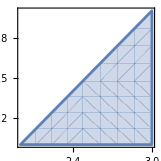

```mathematica
ℛ = ImplicitRegion[(0<x<3)&&(1<y<x-1),{x,y}];

∫_({x,y}∈ℛ) (x+y)
RegionPlot[ℛ]
```

#### Podpunkt b.

0

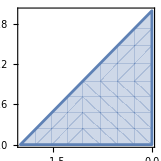

```mathematica
ℛ = ImplicitRegion[(-2<x<0)&&(0<y<x+2),{x,y}];
∫_({x,y}∈ℛ) (x+y)
RegionPlot[ℛ]
```

#### Podpunkt c.

```mathematica
ℛ = ImplicitRegion[(0<x<1)&&(c<y<d),{x,y}];
∫_({x,y}∈ℛ) (x^2+3y)
```

Piecewise[{{1/6 (-2 c-9 c^2+2 d+9 d^2), d>c}, {0, True}}]

#### Podpunkt d.

π/2

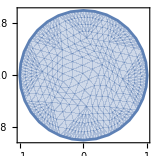

```mathematica
ℛ = ImplicitRegion[x^2+y^2<=1,{x,y}];
∫_({x,y}∈ℛ) (x^2+y^2)
RegionPlot[ℛ]
```

#### Podpunkt e.

(3 π)/2

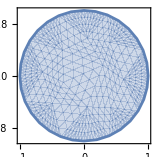

```mathematica
ℛ = ImplicitRegion[x^2+y^2<=1,{x,y}];
∫_({x,y}∈ℛ) ((x-1)^2+y^2)
RegionPlot[ℛ]
```

## Zadanie 7

#### Podpunkt a.

{{y[x]→ⅇ^x C[1]}}

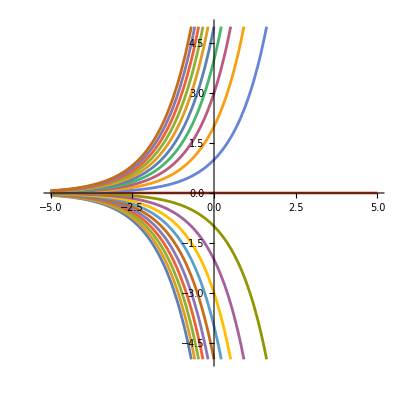

```mathematica
DSolve[y'[x]==y[x]]

solution = DSolve[y'[x]==y[x]&&y[0]==a];
Plot[
Evaluate[y[x]/.solution/.{a->Range[-10,10]}],
{x,-5,5},
PlotRange->{-5,5},
AspectRatio->1
]
```

#### Podpunkt b.

{{y[x]→2 (-1+x)+ⅇ^-x C[1]}}

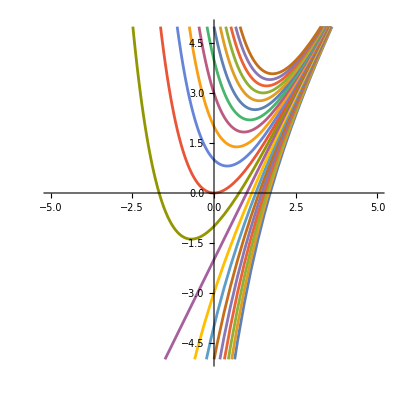

```mathematica
DSolve[y'[x]+y[x]==2x]

solution = DSolve[y'[x]+y[x]==2x&&y[0]==a];
Plot[
Evaluate[y[x]/.solution/.{a->Range[-10,10]}],
{x,-5,5},
PlotRange->{-5,5},
AspectRatio->1
]
```

## Zadanie 8

{{x[t]→ⅇ^t}}

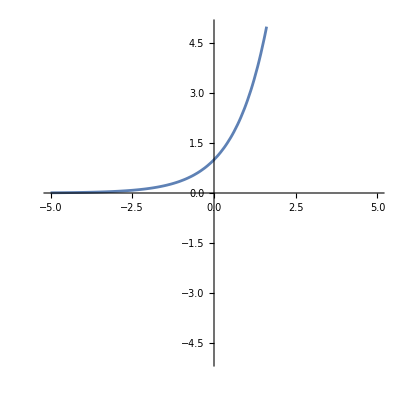

```mathematica
solution = DSolve[x'[t]==x[t]&&x[0]==1]

Plot[
Evaluate[x[t]/.solution],{t,-5,5},
PlotRange->{-5,5},
AspectRatio->1
]
```